## Functions for modeling

### Linear-solid stiffness matrix

cij0[i], Q0[i] are assumed defined for each layer i

```mathematica
cijCarcione[pars_,f0_,ω_]:=Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i}=pars;

{c33i/(-1+√(1+Q01i^2)+(2 ⅈ f0 π Q01i)/ω)+(c11i (2 ⅈ f0 π Q01i+√(1+Q01i^2) ω))/(2 ⅈ f0 π Q01i+(-1+√(1+Q01i^2)) ω)+(2 c44i ω (2 ⅈ f0 π (Q01i-Q02i)+(√(1+Q01i^2)-√(1+Q02i^2)) ω))/((2 ⅈ f0 π Q01i+(-1+√(1+Q01i^2)) ω) (2 ⅈ f0 π Q02i+(-1+√(1+Q02i^2)) ω)),c13i+c11i/(-1+√(1+Q01i^2)+(2 ⅈ f0 π Q01i)/ω)+c33i/(-1+√(1+Q01i^2)+(2 ⅈ f0 π Q01i)/ω)-(2 c44i ω (2 ⅈ f0 π (Q01i+Q02i)+(-2+√(1+Q01i^2)+√(1+Q02i^2)) ω))/((2 ⅈ f0 π Q01i+(-1+√(1+Q01i^2)) ω) (2 ⅈ f0 π Q02i+(-1+√(1+Q02i^2)) ω)),c11i/(-1+√(1+Q01i^2)+(2 ⅈ f0 π Q01i)/ω)+(c33i (2 ⅈ f0 π Q01i+√(1+Q01i^2) ω))/(2 ⅈ f0 π Q01i+(-1+√(1+Q01i^2)) ω)+(2 c44i ω (2 ⅈ f0 π (Q01i-Q02i)+(√(1+Q01i^2)-√(1+Q02i^2)) ω))/((2 ⅈ f0 π Q01i+(-1+√(1+Q01i^2)) ω) (2 ⅈ f0 π Q02i+(-1+√(1+Q02i^2)) ω)),(c44i (2 ⅈ f0 π Q02i+ω+√(1+Q02i^2) ω))/(2 ⅈ f0 π Q02i+(-1+√(1+Q02i^2)) ω),ρi}//N

]
```

### Slowness and L1/L2 matrics

Requires run of the cijCarcione function to get frequency-dependent cij[i]

```mathematica
GetLStovasUrsin[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(c33i/ρi);
β0=√(c44i/ρi);
σ0=1-c44i/c33i;
δ=(c13i-c33i+2c44i)/c33i;
η=(c11i c33i-(c13i+2c44i)^2)/(2 c33i^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));

qα=√(1/α0^2-p^2-p^2 Sα);
qβ=√(1/β0^2-p^2-p^2 Sβ);

L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{qα,qβ},{L1,L2}}

(*l1[j]=L1//N;
l2[j]=L2//N;
q1[j]=qα//N;
q2[j]=qβ//N;*)

]
```

```mathematica
qLCompiled=
Compile[{{cij,_Complex, 1},{ρi,_Real},{p,_Real}},
Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(cij[[3]]/ρi);
β0=√(cij[[4]]/ρi);
σ0=1-cij[[4]]/cij[[3]];
δ=(cij[[2]]-cij[[3]]+2cij[[4]])/cij[[3]];
η=(cij[[1]] cij[[3]]-(cij[[2]]+2cij[[4]])^2)/(2 cij[[3]]^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);
d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));
L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{{qα,0},{0,qβ}},L1,L2}
],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
qL[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=qLCompiled[{c11i, c13i, c33i, c44i}, ρi,p];
```

```mathematica
ClearAll[qL, qLCompiled]
```

```mathematica
RepeatedTiming[Table[GetLStovasUrsin[#,i]&/@cijNums,{i,0,.1,.0001}];]
```

{1.11,Null}

```mathematica
RepeatedTiming[Table[qL[#,i]&/@cijNums,{i,0,.1,.0001}];]
```

{0.039,Null}

```mathematica
cijNums[[5]]
```

{60.2253-0.36254 ⅈ,38.2656-0.0196722 ⅈ,50.9653-0.36254 ⅈ,17.2148-0.171434 ⅈ,2.18}

```mathematica
qLCompiled[cijNums[[1]],1,.1]//Dimensions
```

{3,2,2}

CompiledFunction::cfsa: Argument p at position 3 should be a machine-size real number.

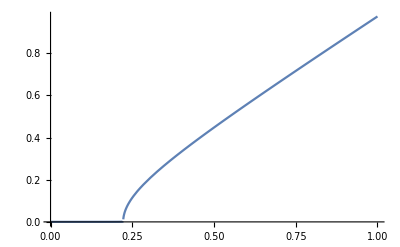

```mathematica
Plot[Evaluate@Im@qL[cijNums[[1]],p][[1,1,1]],{p,0.,1}]
```

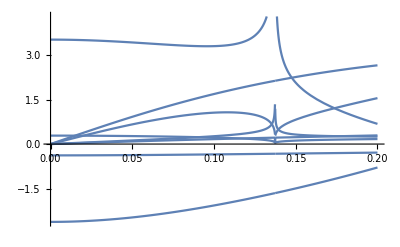

```mathematica
Plot[Re@qL[cijNums[[1]],p],{p,0,.2}]
```

```mathematica
cijNums=cijCarcione[#,150,ωcomp ]&/@model;
```

```mathematica
cijNums
```

{{55.7086-0.0792535 ⅈ,21.3206-0.0303316 ⅈ,55.7086-0.0792535 ⅈ,17.194-0.0244609 ⅈ,2.75},{18.6175-0.114032 ⅈ,10.0496-0.0287088 ⅈ,18.6175-0.114032 ⅈ,4.28395-0.0426618 ⅈ,2.18},{22.5903-0.115238 ⅈ,12.3939-0.0523353 ⅈ,17.3803-0.115238 ⅈ,3.15822-0.0314512 ⅈ,2.38},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22},{60.2253-0.36254 ⅈ,38.2656-0.0196722 ⅈ,50.9653-0.36254 ⅈ,17.2148-0.171434 ⅈ,2.18},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22}}

```mathematica
test=RandomReal[{-1,1},{10,2,2}];
test2=RandomReal[{-1,1},{10}];
```

```mathematica
test2
```

{-0.131156,-0.203295,-0.517515,0.0392209,-0.643401,0.14743,-0.38107,-0.478809,-0.829604,0.817192}

```mathematica
Exp[test[[2]]test2[[2]]]
```

{{1.05737,0.909143},{0.911707,0.864346}}

```mathematica
Exp[test test2]-{{0,1},{1,0}}
```

Thread::tdlen: Objects of unequal length in {{{0.97612,0.981712},{0.981311,1.08656}},«8»,{{0.821694,0.716753},{1.71376,0.456029}}}+{{0,-1},{-1,0}} cannot be combined.

{{0,-1},{-1,0}}+{{{0.97612,0.981712},{0.981311,1.08656}},{{1.05737,0.909143},{0.911707,0.864346}},{{1.41157,1.24303},{1.07733,1.65514}},{{1.01466,1.01174},{1.0079,0.967498}},{{0.842207,1.37895},{1.74914,0.710619}},{{1.11425,0.949119},{0.938401,1.01965}},{{1.15442,0.903316},{1.20719,0.887993}},{{0.794686,0.833284},{0.969008,0.650543}},{{0.68419,0.869403},{1.20621,0.877311}},{{0.821694,0.716753},{1.71376,0.456029}}}

```mathematica
stackRefExperiment2[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray](*;
{transArray,refArray, phaseArray}*)
(*foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
(*;
phaseArray=Exp[ⅈ ω(qABArray d)];
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
]
```

```mathematica
stackRefExperiment[ωcomp,.2,cijs, dList]
```

{{-0.752649+0.0789476 ⅈ,-0.265632+0.0606764 ⅈ},{-0.265632+0.0606764 ⅈ,-0.00371953-0.0309152 ⅈ}}

```mathematica
stackRefExperiment2[ωcomp,.2,cijs, dList]
```

{{-0.752649+0.0789476 ⅈ,-0.265632+0.0606764 ⅈ},{-0.265632+0.0606764 ⅈ,-0.00371953-0.0309152 ⅈ}}

```mathematica
<<CompiledFunctionTools`
```

```mathematica
stackRefExperiment[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L12Array}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray={{Exp[ⅈ ω #1],0},{0,Exp[ⅈ ω #2]}}&@@@(qABArray d);
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
stackRefTransCoefs[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L12Array}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
CArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,2]],L12Array[[;;,1]]}];
DArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,1]],L12Array[[;;,2]]}];
transArray=2Transpose/@ Inverse/@(CArray+DArray);
refArray=1/2 MapThread[#1.#2&,{Transpose/@(CArray-DArray),transArray}];
phaseArray={{Exp[ⅈ ω #1],0},{0,Exp[ⅈ ω #2]}}&@@@(qABArray d);
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
rd[n_Integer,n_Integer,ω_,q_,d_,RT_]:={{0,0},{0,0}};
rd[j_Integer,n_Integer,ω_,q_,d_,RT_]/;j<n:=
rd[j,n,ω,q,d,RT]=e[j,ω,q,d].(RD[j,RT]+Transpose[TD[j,RT]].rd[j+1,n,ω,q,d,RT].Inverse[(IdentityMatrix[2]+RD[j,RT].rd[j+1,n,ω,q,d,RT])].TD[j,RT]).e[j,ω,q,d];
```

```mathematica
cijCarcione[#,150,ωcomp ]&/@model
```

{{55.7086-0.0792535 ⅈ,21.3206-0.0303316 ⅈ,55.7086-0.0792535 ⅈ,17.194-0.0244609 ⅈ,2.75},{18.6175-0.114032 ⅈ,10.0496-0.0287088 ⅈ,18.6175-0.114032 ⅈ,4.28395-0.0426618 ⅈ,2.18},{22.5903-0.115238 ⅈ,12.3939-0.0523353 ⅈ,17.3803-0.115238 ⅈ,3.15822-0.0314512 ⅈ,2.38},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22},{60.2253-0.36254 ⅈ,38.2656-0.0196722 ⅈ,50.9653-0.36254 ⅈ,17.2148-0.171434 ⅈ,2.18},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22}}

```mathematica
synthSand[.4,1,0]
```

{33.6723+0.234433 ⅈ,15.1273+0.319956 ⅈ,33.6671+0.528512 ⅈ,8.0939+0.00479023 ⅈ}

```mathematica
g[#1,#2]&@@@(Transpose[{{1,2,3,4,5},{1,2,3,4,5}}]{2,4,6,8,10})
```

{g[2,2],g[8,8],g[18,18],g[32,32],g[50,50]}

```mathematica
ωcomp
```

```mathematica
cijs=cijCarcione[#,150,ωcomp ]&/@model;
```

```mathematica
test2D
```

{{{-0.11298+0.00119477 ⅈ,-0.246939-0.00159041 ⅈ},{-0.246939-0.00159041 ⅈ,-0.0611467+0.00059957 ⅈ}},{{0.052265-0.00052778 ⅈ,-0.0362943-0.0000159073 ⅈ},{-0.0362943-0.0000159073 ⅈ,0.0283187+0.000343882 ⅈ}},{{0.0151772+0.000840224 ⅈ,0.10158+0.000522018 ⅈ},{0.10158+0.000522018 ⅈ,-0.085141-0.00139516 ⅈ}},{{0.584578-0.736359 ⅈ,-0.00848059+0.159564 ⅈ},{-0.00848059+0.159564 ⅈ,-0.083652-0.0367597 ⅈ}},{{-0.567062+0.782889 ⅈ,-0.151696-0.047801 ⅈ},{-0.151696-0.047801 ⅈ,0.0661361-0.00977077 ⅈ}},{{0.188793-0.000165409 ⅈ,0.130064+0.00062074 ⅈ},{0.130064+0.00062074 ⅈ,-0.0177764-0.000852634 ⅈ}}}

```mathematica
cijs
```

{{55.7086-0.0792535 ⅈ,21.3206-0.0303316 ⅈ,55.7086-0.0792535 ⅈ,17.194-0.0244609 ⅈ,2.75},{18.6175-0.114032 ⅈ,10.0496-0.0287088 ⅈ,18.6175-0.114032 ⅈ,4.28395-0.0426618 ⅈ,2.18},{22.5903-0.115238 ⅈ,12.3939-0.0523353 ⅈ,17.3803-0.115238 ⅈ,3.15822-0.0314512 ⅈ,2.38},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22},{60.2253-0.36254 ⅈ,38.2656-0.0196722 ⅈ,50.9653-0.36254 ⅈ,17.2148-0.171434 ⅈ,2.18},{26.7566-0.100635 ⅈ,12.5179-0.0297369 ⅈ,26.7566-0.100635 ⅈ,7.11936-0.0354491 ⅈ,2.22}}

```mathematica
stackRefExperiment[ωcomp,.6,cijs, dList]//Chop
```

{{8.75624+0.209581 ⅈ,0.29286-8.92734 ⅈ},{0.29286-8.92734 ⅈ,-9.17794-0.421696 ⅈ}}

```mathematica
AbsoluteTiming[Table[stackRefTransCoefs[ωcomp,p,cijs, dList],{p,0,.2,.001}];]
```

{0.307363,Null}

```mathematica
AbsoluteTiming[test=Table[stackRefExperiment2[ωcomp,p,cijs, dList],{p,0,1,.001}];]
```

{0.610917,Null}

```mathematica
ListPlot[test[[;;,1]]]
```

```mathematica
r2[1]
```

{{0.752649-0.0789476 ⅈ,0.265632-0.0606764 ⅈ},{0.265632-0.0606764 ⅈ,0.00371953+0.0309152 ⅈ}}

```mathematica
RTinterface2[.1][[5;;]]
```

{{{{0.961052+0.00034469 ⅈ,0.216255-0.00110857 ⅈ},{-0.214035+0.0010696 ⅈ,0.957494+0.000363555 ⅈ}},{{0.1188+0.000509073 ⅈ,0.128288-0.00126911 ⅈ},{0.128288-0.00126911 ⅈ,-0.141364-0.000385134 ⅈ}}},{{{0.96699-0.000174101 ⅈ,-0.104948-0.000320603 ⅈ},{0.107931+0.00036668 ⅈ,0.963254-0.000237694 ⅈ}},{{-0.192258-0.000584285 ⅈ,-0.127745-0.000128729 ⅈ},{-0.127745-0.000128729 ⅈ,0.211685+0.000844974 ⅈ}}}}

```mathematica
Block[{p=.1},{
rd[1,2,ωcomp,qList[[5;;]],dList[[{1,-1}]],RTinterface2[p][[5;;]]],
stackRefTransCoefs[ωcomp,p,cijs[[5;;6]], dList[[{1,-1}]]]
}]
```

{{{0.1188+0.000509073 ⅈ,0.128288-0.00126911 ⅈ},{0.128288-0.00126911 ⅈ,-0.141364-0.000385134 ⅈ}},{{-0.1188-0.000509073 ⅈ,-0.128288+0.00126911 ⅈ},{-0.128288+0.00126911 ⅈ,0.141364+0.000385134 ⅈ}}}

```mathematica
stackRefTransCoefs[ωcomp,.1,cijCarcione[#,150,ωcomp ]&/@model, dList]
```

{{0.356687-0.0942922 ⅈ,0.145405-0.125876 ⅈ},{0.145405-0.125876 ⅈ,-0.292743+0.0493532 ⅈ}}

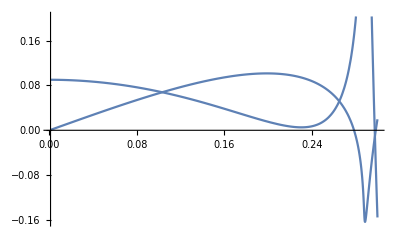

```mathematica
Plot[Re@stackRefTransCoefs[ωcomp,p,cijCarcione[#,150,ωcomp ]&/@model, dList][[3]][[;;,1]],{p,0.001,.3}]
```

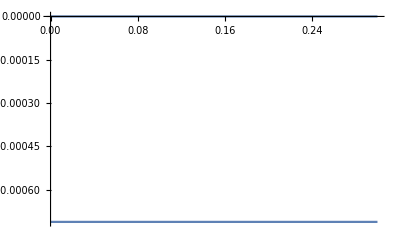

```mathematica
Plot[Im@stackRefTransCoefs[ωcomp,0,cijCarcione[#,150,ωcomp ]&/@model, dList][[3]][[;;,1]],{p,0,.3}]
```

```mathematica
RepeatedTiming[Table[RTinterface2[p],{p,0,.1,.001}];,3]
```

{0.42,Null}

```mathematica
Transpose/@stackRefTransCoefs[ωcomp,.1,cijCarcione[#,150,ωcomp ]&/@model, dList]
```

```mathematica
RTinterface2[.1]
```

### Single interface reflectivity

Requires precomputed L1/L2 matrices and vertical slowness

```mathematica
RT[LBelow_,LAbove_]:=Module[
{L1a=LAbove[[1]],
L1b=LBelow[[1]],
L2a=LAbove[[2]],
L2b=LBelow[[2]],
C,D,inv,RD,RU,TD,TU},

C=Transpose[L2a].L1b;
D=Transpose[L1a].L2b;
inv=Inverse[C+D];
TD=2inv;
RD=(C-D).inv;
(*TU=TDᵀ;
RU=-RD;*)
{TD,RD}//N
];
```

### Stack reflectivity (recursion)

Requires precomputed L1/L2 matrices and vertical slowness and single interface reflectivities.
Note:
1. each layer has the same index as the bottom interface
2. N layers = N interfaces - 1
3. topmost and bottommost layers are half-spaces with zero thickness

```mathematica
q1[j_Integer,q_]:=q[[j,1]];
q2[j_Integer,q_]:=q[[j,2]];
TD[j_Integer,RT_]:=RT[[j,1]];
RD[j_Integer,RT_]:=RT[[j,2]];
dz[j_Integer,d_]:=d[[j]];
```

```mathematica
e[j_Integer,ω_,q_,d_]:=
{
{Exp[(ⅈ ω q1[j,q] dz[j,d])],0},
{0,Exp[(ⅈ ω q2[j,q] dz[j,d])]}
};

rd[n_Integer,n_Integer,ω_,q_,d_,RT_]:={{0,0},{0,0}};

rd[j_Integer,n_Integer,ω_,q_,d_,RT_]/;j<n:=
rd[j,n,ω,q,d,RT]=e[j,ω,q,d].(RD[j,RT]+Transpose[TD[j,RT]].rd[j+1,n,ω,q,d,RT].Inverse[(IdentityMatrix[2]+RD[j,RT].rd[j+1,n,ω,q,d,RT])].TD[j,RT]).e[j,ω,q,d];
```

```mathematica
ClearAll[phaseFactor];
phaseFactor[ω_,d_/;ArrayQ[d]]:=;
```

```mathematica
ArrayQ[{{1,2,3,45},{1,23,3}}]
```

False

## Stovas and Ursin (2003) and Ursin and Stovas (2002) reflectivity examples

### Rock Physics Input

```mathematica
someFunction[fractureDensity_, waterSaturation_, {ω_,τ0_}]:=Out[{c11, c13, c33, c44, ρbulk}]
```

```mathematica
M[ω]
```

### Declare model

3 interfaces: [number of the interface]
-> chalk/shale (iso)			[1]
-> shale/sandstone (vti) 		[3]
-> siltstone/sandstone (vti)	[5]

Model parameters : {c11, c13, c33, c44, ρ, Q1, Q2}

```mathematica
model={
(*chalk (iso)*)
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,350,350}/.vp->4.5/.vs->2.5/.den->2.75,
(*shale (iso)*)
{vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,100,50}/.vp->2.92/.vs->1.4/.den->2.18,
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100},
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100}
};
```

Layer thickness is computed randomly for further tests

```mathematica
dList=
Join[{0},SeedRandom[2018];RandomReal[{0,.1},Length[model]-2],{0}];
```

```mathematica
model[[1]]//Length
```

7

```mathematica
RTinterface2[.1]//Length
```

6

Get frequency-dependent cij, matrices L1/L2 and slowness for a given f0 and a given signal frequency f

```mathematica
f0=150;
f=40;
ωcomp=2Pi f;

qList=ConstantArray[0,{Length[model],2}];
LList=ConstantArray[0,{Length[model],2,2,2}];

Table[
{qList[[i]],LList[[i]]}=GetLStovasUrsin[
cijCarcione[model[[i]],f0,ωcomp]
,p];
,{i,1,Length[model]}
];
```

```mathematica
qp[p_, f_:f0,ω_:ωcomp]:=GetLStovasUrsin[cijCarcione[#,f,ω],p]&/@model;
```

```mathematica
RTinterface2[p_, f_:f0, ω_:ωcomp]:=Module[{q,L},
{q,L}=Transpose@qp[p,f, ω];
MapThread[RT,{RotateLeft@L,L}]
];
```

```mathematica
SetAttributes[RTinterface2, Listable]
```

```mathematica
ClearAll@RTinterface2
```

```mathematica
Plot3D[Re@RTinterface2[s,f0,ω][[1,1,1,1]],{s,0,.1},{ω,2π 10,2π 200}]
```

Calculate reflection-transmission coefficients for each interface

```mathematica
Clear[RTinterface];
```

```mathematica
RTinterface[i_]:=
RT[LList[[i+1]],LList[[i]]];
```

```mathematica
pvec=Table[p,{p,0,.3,.0025}];
rtest=Table[RTinterface[i,#],{i,1,Length@model-1}][[2,2]]&/@pvec;
```

```mathematica
Table[RTinterface[i,#],{i,1,Length@model-1}][[2,2]]&/@pvec[[1;;2]]
```

{{{((1) (-((18-1) 5 1)/(√(1+1) √1)+4))/(-1. (-1/(√(1+1) 1)+1+1-1/1) (5+1/1)11)+1/1,1},{1}},1}
 |  |  |  |

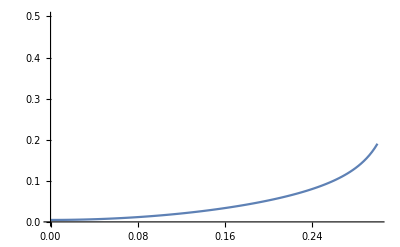

```mathematica
ListPlot[{pvec,-Re@rtest[[All,1,1]]}ᵀ,Joined->True,PlotRange->{{0,0.3},{0,.5}}]
```

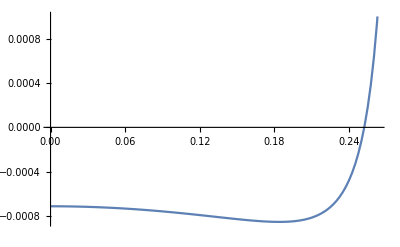

```mathematica
ListPlot[{pvec,Im@rtest[[All,1,1]]}ᵀ,Joined->True,PlotRange->{{0,0.3},{0.001,-.008}}]
```

Calculate the response of the stack at a fixed p

```mathematica
Block[{p=.1},rd[1,Length[model],ωcomp,qList,dList,RTinterface2[p]]//N]
```

{{0.356687-0.0942922 ⅈ,0.145405-0.125876 ⅈ},{0.145405-0.125876 ⅈ,-0.292743+0.0493532 ⅈ}}

## Stovas and Ursin (2003) Well - log example

### Load and prepare the data

Null

```mathematica
Null
```

```mathematica
Null
```

Null

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

### Calculate the RT response

#### for a fixed frequency/slowness pair

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

#### for a range of frequency / wavenumbers

predefine arrays

```mathematica
fList=Table[i,{i,1,101,.5}];
pList=Table[i,{i,0,.25,.00125}];
kList=Table[2Pi fList[[fj]]pList[[pj]],{fj,1,Length[fList]},{pj,1,Length[pList]}];

output=ConstantArray[0,{Length[fList],Length[pList],2,2}];
```

loop over frequency/wavenumber

```mathematica
If[Length[fList]≥Length[pList],
listLong=fList;listShort=pList;
writeOut[jS_,jL_,writeFrom_]:=output[[jL,jS]]=writeFrom;
pf[jS_,jL_]:={pList[[jS]],fList[[jL]]}
,
listLong=pList;listShort=fList;
writeOut[jS_,jL_,writeFrom_]:=output[[jS,jL]]=writeFrom;
pf[jS_,jL_]:={pList[[jL]],fList[[jS]]};
];
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null